```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
Needs["ErrorBarLogPlots`"] (* this has to be installed separately*)
Clear[SE]
SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]
```

### import experimental data:

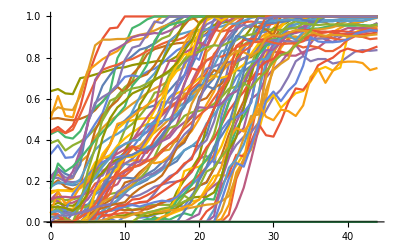

```mathematica
expr=Import[NotebookDirectory[]<>"data_Fig_4\\flat_R_fraction_RIF_1ug.txt","Table"];
expr=Table[Table[{t-1,expr[[i,t]]},{t,Length[expr[[i]]]}],{i,Length[expr]}];
ListPlot[expr,Joined->True]
```

## Fig . S4A

### select wells for which the initial fraction of red cells is between 0.1 and 0.4:

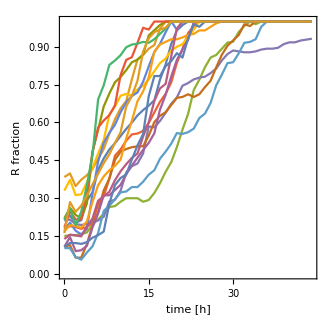

```mathematica
exprsel=Select[expr,(#[[1,2]]>=0.1 && #[[1,2]]<=0.4)&];
ListPlot[exprsel,Joined->True,Frame->True,FrameLabel->{"time [h]","R fraction"},ImageSize->330,AspectRatio->1,FrameStyle->Black,BaseStyle->{FontSize->18}]
```

## Fig . S4B

### computer model: no adhesion , different initial ratios, selected at T = 19 h

```mathematica
AllelesSizes[name_]:=Module[{names,frames,secsizes,tmp,framelengths},names=FileNames[NotebookDirectory[]<>"data_Fig_4\\"<>name<>"\\types_*.dat"];
frames=Table[tmp=ReadList[names[[i]],{Number,Number,Number,Number}];{Select[tmp,(#[[2]]==0)&],Select[tmp,(#[[2]]==1)&]},{i,Length[names]}];
framelengths=Length[#]&/@frames;
If[ProcessDataVerbose,Print[Length[frames]," max_len=",Max[framelengths]," n=",Count[framelengths,Max[framelengths]]]];
frames[[All,All,All,{1,4}]] (* indices: runs, alleles,times, time/size *)
]
```

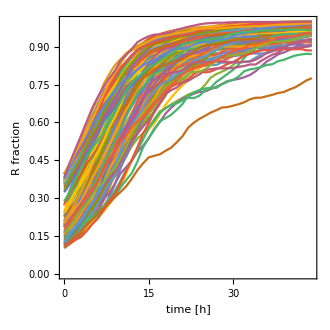

```mathematica
ss="08";  (* this gives the best fit *)
modelcurves=Flatten[(tmp=Select[AllelesSizes[#],(Min[Length[#[[1]]],Length[#[[2]]]]>20+44)&];Table[Table[{tmp[[r,1,t,1]]-19,1.tmp[[r,2,t,2]]/(tmp[[r,1,t,2]]+tmp[[r,2,t,2]])},{t,20,20+44}],{r,Length[tmp]}])&/@{"100x110_RIF_DT_3h_ini19h_no_adh_s"<>ss<>"_1in10att0_sin_P10_A0","100x110_RIF_DT_3h_ini19h_no_adh_s"<>ss<>"_1in5att0_sin_P10_A0","100x110_RIF_DT_3h_ini19h_no_adh_s"<>ss<>"_1in2.5att0_sin_P10_A0"},1];
ListPlot[Select[modelcurves,(#[[1,2]]>0.1 && #[[1,2]]<0.4)&],Joined->True,Frame->True,FrameLabel->{"time [h]","R fraction"},ImageSize->330,AspectRatio->1,FrameStyle->Black,BaseStyle->{FontSize->18}]
```

## Fig . S4C

```mathematica
Clear[AverageRuns]
AverageRuns[d_]:=Module[{tmp2=Gather[d,(Floor[#1[[1]]]==Floor[#2[[1]]])&]},
{{Mean[#[[All,1]]],Mean[#[[All,2]]]},ErrorBar[SE[#[[All,2]]]]}&/@tmp2]
```

### select model curves that have the same distribution of initial red fraction as experimental curves:

{0.212765957446808512,0.383512544802867395,0.149825783972125426,0.178321678321678334,0.211469534050179209,0.106761565836298936,0.101754385964912278,0.329749103942652333,0.107266435986159175,0.219931271477663226,0.183745583038869259,0.17437722419928825,0.168421052631578944,0.137809187279151951,0.214035087719298245,0.108013937282229966,0.161403508771929827}

{20,60,61,63,65,95,100,103,124,125,134,137,2,19,41,48,57,68,81,51,58,67,73,97,98,102,20,60,61,63,65,95,100,8,11,12,17,22,23,25,29,38,40,42,45,59,66,74,79,8,11,17,21,22,23,29,37,38,40,42,45,46,66,74,105,116,119,132,8,11,12,17,22,23,25,38,40,42,45,59,66,74,79,52,65,70,75,89,95,51,58,64,67,73,86,87,97,102,58,77,98,102,62,77,82,85,92,98,101,102,1,2,4,28,43,48,57,68,78,20,60,63,65,70,95,100,8,11,12,13,17,22,23,25,38,40,42,45,59,66,74,79,19,62,77,81,82,85,92,98,101}

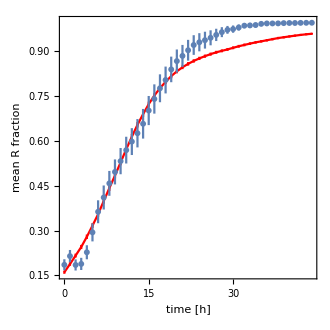

chi2=17.2202

```mathematica
exprini=exprsel[[All,1,2]]
modelindices=Flatten[Table[Select[Table[{Abs[exprini[[i]]-modelcurves[[j,1,2]]],j},{j,Length[modelcurves]}],(#[[1]]<0.01)&],{i,Length[exprini]}],1][[All,2]]
avtheory=AverageRuns[Flatten[modelcurves[[modelindices]],1]];
avexpr=AverageRuns[Flatten[exprsel,1]];
Show[ErrorListPlot[avtheory,PlotStyle->{Red},Joined->True],ErrorListPlot[avexpr],PlotRange->All,Frame->True,FrameLabel->{"time [h]","mean R fraction"},ImageSize->330,AspectRatio->1,FrameStyle->Black,BaseStyle->{FontSize->18}]
Print["chi2=",Mean[(Abs[avtheory[[All,1,2]]-avexpr[[All,1,2]]]^2)/(avtheory[[All,2,1]]^2+avexpr[[All,2,1]]^2)]]
```